# Tech Project 2

## Derivatives

Kyle Tolliver

```mathematica
D[Sqrt[3Cos[4x^2+4x-7]],x]
```

-(√3 (-4-8 x) Sin[7-4 x-4 x^2])/(2 √Cos[7-4 x-4 x^2])

```mathematica
D[(3x^2-4x+14)/Sqrt[x-5],x]//Simplify
```

(26-64 x+9 x^2)/(2 (-5+x)^(3/2))

```mathematica
f[x_] := 8.3Sin[x]-4.2Cos[x]
```

```mathematica
f'[x]
```

8.3 Cos[x]+4.2 Sin[x]

```mathematica
f'[5π/8]
```

0.704022

```mathematica
f[x_] =  x^2-Log[x-1]
```

x^2-Log[-1+x]

```mathematica
f'[x]
```

-1/(-1+x)+2 x

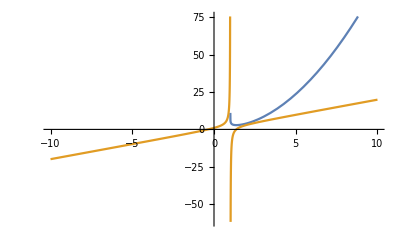

```mathematica
Plot[{f[x],f'[x]},{x,-10,10}]
```

```mathematica
Solve[D[(x^2)Cos^2[y[x]]-Sin[y[x]] == (e^5x)+(6y[x] √x),x],y'[x]]
```

{{y'[x]→-(-e^5 √x+2 Cos^(2[y[x]]) x^(3/2)-3 y[x])/(√x (-6 √x-Cos[y[x]]))}}